```mathematica
(* Method of moments estimator *)
(*Function to generate rate matrix from an edge list and weights*)RateMatrix[edges_List,weights_List,n_Integer]:=Module[{Q},Q=ConstantArray[0,{n,n}];
Do[Q[[edges[[i,1]],edges[[i,2]]]]=weights[[i]],{i,Length[edges]}];
Do[Q[[i,i]]=-Total[Q[[i,All]]],{i,n}];
Q];

(*Function to compute steady-state probabilities*)
SteadyStateProbabilities[Q_]:=Module[{n,A,b,π},n=Length[Q];
A=Append[Transpose[Q],ConstantArray[1,n]];
b=Append[ConstantArray[0,n],1];
π=LinearSolve[A,b];
π];

(*EPssSymbolic[Q] returns the symbolic entropy-production rate*)EPss[Q_?MatrixQ]:=Module[{n=Length[Q],π,sol,expr},(*reuse the π-symbols*)π=Array[Symbol["π"<>ToString[#]]&,n];
sol=Solve[Join[Table[Sum[π[[k]] Q[[k,j]],{k,1,n}]==0,{j,1,n}],{Total[π]==1}],π];
(*build the double sum ∑_{i,j}[π_i Q_{ij}-π_j Q_{ji}] Log[(π_i Q_{ij})/(π_j Q_{ji})]*)expr=Sum[(π[[i]]*Q[[i,j]]-π[[j]]*Q[[j,i]])*Log[(π[[i]]*Q[[i,j]])/(π[[j]]*Q[[j,i]])],{i,1,n},{j,1,n}];
(*substitute in π-solution,divide by 2,and simplify*)
Simplify[(expr/. sol[[1]])/2]
];

(*Function to compute mean first passage times*)
MeanFirstPassageTimes[Q_]:=Module[{n,Z,T},n=Length[Q];
ss = SteadyStateProbabilities[Q];
Pss = Table[ss, {i,n}];
Z=Inverse[Pss-Q]-Pss;
T=Table[(Z[[j,j]]-Z[[i,j]])/ss[[j]],{i,n},{j,n}];
Simplify[T]];

MeanFirstPassageTimes2[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-ConstantArray[1,n-1];(*-1 vector*)(*Solve Qsub x=-1*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[T];];

VarianceFirstPassageTimes[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
m = MeanFirstPassageTimes2[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-2*m[[subIdxs,j]];(*-1 vector*)(*Solve Qsub x=-2m*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]] - m[[i,j]]^2;],{i,1,n},{j,1,n}];
Return[T];];

LaplaceTransformFPT[Q_,s_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];
(*T[[i,j]] will store phi_{i->j}(s)=E[e^{-s T_{i->j}}].*)Do[If[i==j,(*By definition,time from j to j is 0=>Laplace transform=E[e^{-s*0}]=1*)
T[[i,j]]=1,(*i!=j:solve the submatrix system (Q+sI)_{S' x S'}*phi_{S'}=-Q_{S',j},using the boundary condition phi_j(s)=1.*)
subIdxs=Delete[Range[n],j];(*states except j*)
Qsub=Q[[subIdxs,subIdxs]]-s*IdentityMatrix[n-1];
(*Build the inhomogeneous RHS=-Q[i,j],for each i in subIdxs*)rhs=Table[-Q[[subIdxs[[row]],j]],{row,1,n-1}];
x=LinearSolve[Qsub,rhs];
(*x gives phi_{k->j}(s) for k in subIdxs.We want the component corresponding to i.*)T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[FullSimplify[T]];];

LaplaceTransformToSetByState[Q_,start_,hit_List,s_]:=Module[{n=Length[Q],subStates,m,results,eqMatrix,eqRHS,hj,sol,iPos},(*If'start' is already in'hit',then the time is 0 with prob=1=>transform=1,but specifically we don't "hit h_j first" if j!=that state.We'll handle it below.*)If[MemberQ[hit,start],(*Then we trivially return a vector of dimension Length[hit],where the entry for'start' is 1,and all others 0.*)
Return[Map[If[#==start,1,0]&,hit]]];
(*Otherwise,we solve one linear system for each h_j in'hit'.*)
subStates=Complement[Range[n],hit];(*non-absorbing set*)m=Length[subStates];
results=Table[((*Build the (Q-sI) submatrix for non-absorbing states.*)eqMatrix=Table[Q[[subStates[[i]],subStates[[j]]]],{i,m},{j,m}];
Do[eqMatrix[[i,i]]-=s,{i,1,m}];
(*RHS=-Q_{i,h_j},for each i in subStates.*)
eqRHS=Table[-Q[[subStates[[i]],hj]],{i,1,m}];
(*Solve and get phi_i^(j)(s).Then extract the'start' component.*)
sol=LinearSolve[eqMatrix,eqRHS];
iPos=First@Position[subStates,start];
sol[[iPos]]),{hj,hit}  (*for each absorbing state in'hit'*)];
Return[results];];

LogSpecificity[c_,ω_,γ_,rates_,edges_]:= Module[{n,Q, weights,ss,kboff,konb,kuon,kbon,koffu,kuoff,konu},
{kboff,konb,kuon,kbon,koffu,kuoff,konu} = Table[rates[[i]][[1]]/.rates[[i]],{i,1,Length[rates]}];
weights={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb,konu};
Q = RateMatrix[edges, weights,6];
ss = SteadyStateProbabilities[Q];
Log[ss[[3]]/ss[[5]]] + Log[ω/γ]
];
LogSpecificityFull[c_,ω_,γ_,rates_,edges_]:= Module[{n,Q, weights,ss,kboff,konb,kuon,kbon,koffu,kuoff,konu,koffb},
{kboff,konb,kuon,kbon,koffu,kuoff,konu,koffb} = Table[rates[[i]][[1]]/.rates[[i]],{i,1,Length[rates]}];
weights={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb,konu,koffb,koffb};
Q = RateMatrix[edges, weights,6];
ss = SteadyStateProbabilities[Q];
Log[ss[[3]]/ss[[5]]] + Log[ω/γ]
]
```

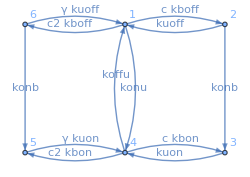

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {6,1,2};
onStates = {5,4,3};
Foff1on = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = Foff1on[[3]][[1]]*F31 +Foff1on[[2]][[1]]*F41 + Foff1on[[1]][[1]]*F51; (*F1off[[2]][[1]]*F41 +*)
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
rates={c>0,c2>0,γ>0,kboff>0,konb>0,kuon>0,kbon>0,koffu>0,kuoff>0,konu>0};
assum=And@@rates;
expr0 = Simplify[FoffOn];
expr1=Together[expr0]//Cancel;
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2];
exprS12PartEval = exprS12 /.{c2->10,γ->10};
exprS12PartEvalSimpl = Simplify[exprS12PartEval];

(*Pjoint=InverseLaplaceTransform[exprS12PartEvalSimpl,{s1,s2},{t1,t2},Assumptions->assum];*)(*~35s*)
```

```mathematica
τfun[c_,c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_ ]:=Evaluate[τ];
FoffOnfun[c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_ ]:=Evaluate[FoffOn];
```

```mathematica
Clear[FisherSafe]
Clear[FisherRate]

FisherRate[c0i_,c2i_,γi_,kboffi_,konbi_,kuoni_,kboni_,koffui_,kuoffi_,konui_ ]:=Module[{FoffOnPartEval,PjointPartEval,d2LogPjointPartEval,τPartialEval,Fjoint,Pjoint,integrand,integral},
FoffOnPartEval=FoffOnfun[c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui] ;
τPartialEval=τfun[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];

PjointPartEval=InverseLaplaceTransform[FoffOnPartEval,{s1,s2},{t1,t2}];
d2LogPjointPartEval=D[Log[PjointPartEval],{c,2}];
integrand=Evaluate[PjointPartEval* d2LogPjointPartEval/.c->c0i];

Compile[{{t1,_Real},{t2,_Real}},integrand,CompilationTarget->"C"];
integral=-NIntegrate[integrand,{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->10];
c0i^2*integral/τPartialEval
];

FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherRate[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvs}
],{NIntegrate::ncvs}
];
```

```mathematica
kmin =0.00001;
kmax = 5;
kdl=0.0888;
c0=100;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
FisherSafe[c0,0.1,1,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.802289

```mathematica
FisherSafeLog[c_,c2_,γ_,lnkboff_,lnkonb_,lnkuon_,lnkbon_,lnkoffu_,lnkuoff_,lnkonu_]:=FisherSafe[c,c2,γ,Exp[lnkboff],Exp[lnkonb],Exp[lnkuon],Exp[lnkbon],Exp[lnkoffu],Exp[lnkuoff],Exp[lnkonu]];
```

```mathematica
ln5 = Log[5];
lnkdl=Log[0.0888];
lnkmin=-5;

{res,data}=Reap[
NMaximize[{FisherSafeLog[40,0,1,lnkboff,ln5,ln5,lnkbon,ln5,lnkuoff,lnkonu],
lnkmin<lnkboff<lnkdl,
lnkmin<lnkbon<lnkdl,
lnkmin<lnkuoff<ln5,
lnkmin<lnkonu<ln5},
{lnkboff,lnkbon,lnkuoff,lnkonu},
Method->"DifferentialEvolution",PrecisionGoal->6,AccuracyGoal->6,MaxIterations->5,EvaluationMonitor:>Sow[{lnkboff,lnkbon,lnkuoff,lnkonu}]]];
```

$Aborted

```mathematica
kmin =0.0001;
kmax = 5;
kdl=0.0888;

{res,data}=Reap[
NMaximize[{FisherSafe[1,0,1,kboff,5,5,kbon,5,kuoff,konu],
kmin<=kboff<=kdl,
kmin<=kbon<=kdl,
kmin<=kuoff<=5,
kmin<=konu<=5},
{kboff,kbon,kuoff,konu},
Method->"DifferentialEvolution",PrecisionGoal->6,AccuracyGoal->6,MaxIterations->5,EvaluationMonitor:>Sow[{lnkboff,lnkbon,lnkuoff,lnkonu}]]];
```

```mathematica
res
```

{0.0521318,{kboff→0.0888,kbon→0.0666011,kuoff→0.860533,konu→0.0373274}}

```mathematica
818/60.
```

13.6333

```mathematica
FindMaximum[FisherSafe[1,0,1,kboff,5,5,kbon,5,kuoff,konu],
{{kboff,1.1*kmin,kmin,kdl},{kbon,1.1*kmin,kmin,kdl},{kuoff,4.9,kmin,kmax},{konu,4.9,kmin,kmax}},
Method->"ConjugateGradient",PrecisionGoal->5,AccuracyGoal->5,MaxIterations->10];
```

```mathematica
(*Dummy function*)
expr= x+a+2;
exprFun[a_]:=Evaluate[expr];
Foo[xi_,ai_]:=Module[{exprPartEval},
(*exprPartEval=expr /. a->ai;*)
exprPartEval=exprFun[ai];
exprPartEval = Simplify[exprPartEval^2];
exprPartEval = exprPartEval /. x->xi
];
```

```mathematica
Foo[1,2]
```

25

```mathematica
(*Numerical inverse Laplace*)
(* ::Package::*)(*InverseLaplace2D:Numerically inverts F(s1,s2) to f(t1,t2) via the double Bromwich integral f(t1,t2)=1/(2πi)^2 ∫_{Re s1=c1} ∫_{Re s2=c2} e^{s1 t1+s2 t2} F(s1,s2) ds2 ds1 Usage:InverseLaplace2D[F,t1,t2] uses defaults c1=c2=1.0 InverseLaplace2D[F,t1,t2,c1,c2] specify your shifts c1,c2 InverseLaplace2D[...,opts] extra options passed to NIntegrate Note:c1,c2 must exceed the real parts of all singularities of F.*)

ClearAll[InverseLaplace2D];
Options[InverseLaplace2D]={Method->{"DoubleExponential"},MaxRecursion->6,PrecisionGoal->6};

InverseLaplace2D[
Ffunc_,
t1_?NumericQ,t2_?NumericQ,
c1_?NumericQ:1.0,c2_?NumericQ:1.0,
opts:OptionsPattern[]]:=Module[{w1,w2},
1/(4 Pi^2)*
NIntegrate[
Exp[(c1+I w1) t1+(c2+I w2) t2]*
Ffunc[c1+I w1,c2+I w2],
{w1,-∞,∞},{w2,-∞,∞},
Method->OptionValue[Method],
MaxRecursion->OptionValue[MaxRecursion],
PrecisionGoal->OptionValue[PrecisionGoal],
Evaluate[FilterRules[{opts},Options[NIntegrate]]]]
];

(*---Simple tests---*)

(*1) F(s1,s2)=1/(s1 s2)==>f(t1,t2)=1*)
F1[s1_,s2_]:=1/(s1*s2);
Print["Test 1: F=1/(s1 s2), f should be 1: ",N[InverseLaplace2D[F1,1.0,2.0],6]];

(*2) F(s1,s2)=1/((s1+a)(s2+b))==>f(t1,t2)=Exp[-a t1-b t2]*)
a=1.0;b=2.0;
F2[s1_,s2_]:=1/((s1+a)*(s2+b));
tvals={0.5,1.3};
numeric=InverseLaplace2D[F2,tvals[[1]],tvals[[2]],a+0.5,b+0.5];
analytic=Exp[-a*tvals[[1]]-b*tvals[[2]]];
Print["Test 2: F=1/((s1+1)(s2+2)), at (t1,t2)=",tvals,"\n   numerical = ",N[numeric,6],"\n   analytic  = ",N[analytic,6]];
```

Test 1: F=1/(s1 s2), f should be 1: InverseLaplace2D[F1,1.,2.]

Test 2: F=1/((s1+1)(s2+2)), at (t1,t2)={0.5,1.3}
   numerical = InverseLaplace2D[F2,0.5,1.3,1.5,2.5]
   analytic  = 0.0450492

```mathematica
(*Define a two-argument function*)
f12[s1_,s2_]:=1/(s1 s2);

(*Now this will return≃1.0*)
InverseLaplace2D[f12,2.0,0.8,3.5,5.5]
```

InverseLaplace2D[f12,2.,0.8,3.5,5.5]